```mathematica
ClearAll["Global`*"]

(*aux: type punning*)
signedToUnsigned[x_, b_:32]:=Module[{val=x, bits=b},
If[Negative[val],
nd=IntegerDigits[val,2];                                                  (* truncate extra digits *)
If[Length[nd]>bits,val=FromDigits[Take[nd,-bits],2],val];
val=Abs[val];                                                                            (* 1's complement *)
n=BitXor[val,FromDigits[ ConstantArray[1,bits],2]];
n+=1,                                                                                             (* 2's complement *)
(* else, nothing to do, just truncate it to spec bits *)
nd=IntegerDigits[val,2];                                                  (* truncate extra digits *)
If[Length[nd]>bits,val=FromDigits[Take[nd,-bits],2],val];
val]
];
realToInt32[x_]:=Module[{xx=x},
realbits=IntegerDigits[xx,2];
If[Length[realbits]>32,
int32bits=Take[realbits,-32];  (* take last 32 slots, aka first for 32bits *)
int32=FromDigits[int32bits,2];
int32, (*else*)
xx]
];

(*convert samples from 0-1 to -1-+1*)
convertSample[kx_]=2.0*kx-1.0;
```

```mathematica
(* -- Owen Scrambled Sobol -- *)
Clear[ossC0,ossC1,ossC2,ossC3,ossC4,ossC5,ossC6,ossC7]
ossC0=signedToUnsigned[0];
ossC1=signedToUnsigned[1];
ossC2=signedToUnsigned[Interpreter["HexInteger"]["80000000"]];
ossC3=signedToUnsigned[1664525];
ossC4=signedToUnsigned[1013904223];
ossC5=signedToUnsigned[1103515245];
ossC6=signedToUnsigned[12345];
ossC7=signedToUnsigned[31];
ossC8=signedToUnsigned[Interpreter["HexInteger"]["ffffffff"]];

lcG1[kn_Integer]:=Module[{n=signedToUnsigned[kn]},signedToUnsigned[n*ossC3+ossC4]];
lcG2[kn_Integer]:=Module[{n=signedToUnsigned[kn]},signedToUnsigned[n*ossC5+ossC6]];

sobolS[kn_Integer]:=Module[{n=signedToUnsigned[kn]},
px=ossC0;
py=ossC0;
dx=ossC2;
dy=ossC2;

While[n≠ossC0,
cc=BitAnd[n,ossC1];
If[BitAnd[n,ossC1]≠ossC0,
px=BitXor[px,dx];py=BitXor[py,dy]];
dx=BitShiftRight[dx,ossC1];
dy=BitXor[dy,BitShiftRight[dy,ossC1]];
n=BitShiftRight[n,ossC1];
];
{px,py}
]

owenScramble[kp_Integer, ks_Integer]:=Module[{p=signedToUnsigned[kp],
                                                                                                    s=signedToUnsigned[ks]},
s=lcG2[s];
For[i=BitShiftLeft[ossC1,ossC7],i>ossC0,i=BitShiftRight[i,ossC1],
If[s>ossC2,p=BitXor[p,i]];
If[BitAnd[p,i]==ossC0,s=lcG1[s],s=lcG2[s]];
];
p
]

owenScrambledSobol[kidx_Integer]:=Module[{idx=kidx},
ss=sobolS[idx];
s1=owenScramble[ss[[1]],42]/ossC8;
s2=owenScramble[ss[[2]],666]/ossC8;
{s1,s2}//N
]

owenScrambledSobol[12345]
```

{0.258932,0.0576359}

```mathematica
Manipulate[Module[{data,inside,insidepts},SeedRandom[n];
(*data=RandomReal[{-1,1},{m,2}];*)
rdata=ParallelArray[owenScrambledSobol,m];
data=Map[convertSample,rdata];
insidepts=Cases[data,{x_,y_}/;x^2+y^2<1];
inside=Length[insidepts];
Text@Style[Column[{Graphics[{PointSize[0.006],RGBColor[0.93,0.24,0.29],Disk[{0,0},1],Black,Point[data]},ImageSize->If[format,500,350]],Row[{"inside: ",inside,"\toutside: ",m-inside,"\ttotal:  ",m}],Row[{"π ≈ 4 × ",inside,"/",m," = ",4. inside/m}]}],"Label"]],{{n,1,"random seed"},1,1000,1},{{m,1,"sample size"},64,8192,64,Appearance->"Labeled"},{{format,False,"large format"},{True,False}},AutorunSequencing->{1,2}]
```

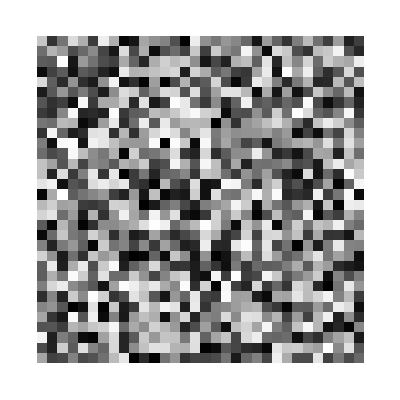

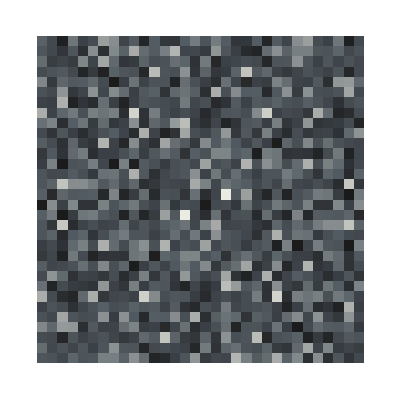

```mathematica
Clear[a,ar, arf, arfp];
a=Array[owenScrambledSobol,512]; (*32/8, 128/16, 512/32*)
ar=RandomSample[a]; (*randomize sample order, ie inderx*)
arf=Flatten[ar];
arfp=Partition[arf,32];
ArrayPlot[arfp]
ArrayPlot[Abs[RotateLeft[Fourier[arfp-.5],{16,16}]],ColorFunction->"GrayTones"]
```

see Perrrier et al. 2018 where from Owen Scrambled Sobol they get to blue noise!
also see.. https://perso.liris.cnrs.fr/david.coeurjolly/publications/heitz19.html to distribute OSS as blue noise